## Plotting the Copying function

### Type I

```mathematica
Copying[β_,y_]:=y^β/(y^β+(1-y)^β);
```

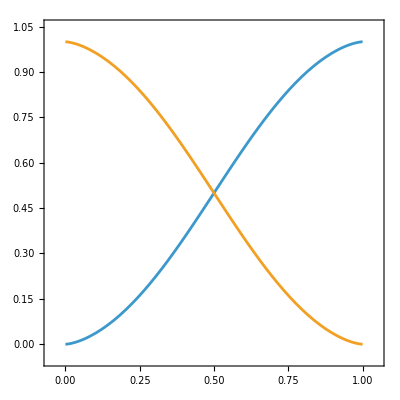

```mathematica
Plot[Evaluate[Table[Copying[β,y],{β,{1.5,-1.5}}]],{y,0,1},PlotRange->{{-0.05,1.05},{-0.05,1.05}},Frame->True,AspectRatio->1]
```

### Type II

```mathematica
m=2;(*Number of morphs*)
factor=1.2;(*Conformism/anticonformism factor*)
kindofcopying=.;(*What kind of copying? conformism or anticonformism*)
```

```mathematica
chooseD[y_,kindofcopying_]:=1/factor If[kindofcopying=="conformism",(1/Max[y]-1) ∑_(j=1)^m If[y⟦j⟧>1/m,y⟦j⟧,0],-∑_(j=1)^m If[y⟦j⟧>1/m,y⟦j⟧,0]];
whichC[yi_,y_,kindofcopying_]:=
Which[yi==0,yi,yi==1,yi,yi==1/m,yi,
yi>1/m,yi+chooseD[y,kindofcopying] yi/(∑_(j=1)^m If[y⟦j⟧>1/m,y⟦j⟧,0]),
yi<1/m,yi-chooseD[y,kindofcopying] (1/yi)/(∑_(j=1)^m If[y⟦j⟧<1/m,1/y⟦j⟧,0])]
```

```mathematica
Copyingcomplex[y_,kindofcopying_]:=Table[whichC[y⟦i⟧,y,kindofcopying],{i,1,m,1}];
```

```mathematica
result={};
For[j=0,j<=1,j=j+0.01,For[k=0,k<=1,k=k+0.01,If[j+k==1.0,AppendTo[result,{j,k}]]]];
result//Chop;
```

```mathematica
cpresultconformism=Copyingcomplex[#,"conformism"]&/@result;
cpresultanti=Copyingcomplex[#,"anticonformism"]&/@result;
```

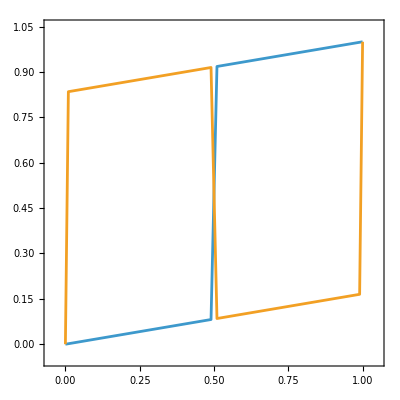

```mathematica
ListPlot[{Table[{result⟦All,1⟧⟦i⟧,cpresultconformism⟦All,1⟧⟦i⟧},{i,1,Length[result]}],Table[{result⟦All,1⟧⟦i⟧,cpresultanti⟦All,1⟧⟦i⟧},{i,1,Length[result]}]},Joined->True,PlotRange->{{-0.05,1.05},{-0.05,1.05}},Frame->True,AspectRatio->1]
```